# Ejercicios 1

## Programa

```mathematica
(*programa para máximos y mínimos*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

## 13

```mathematica
(*programa para máximos y mínimos*)
(*ejericio #13*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
```

```mathematica
f=(2 x^2)/(x-2);
```

Maximo en =  0.

Minimo en x = 4.

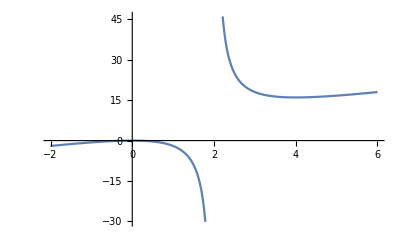

```mathematica
maxminint[f,-∞,∞]
```

## 14

```mathematica
(*programa para máximos y mínimos*)
(*ejericio #14*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

```mathematica
f= 1-x-(x^2-1);
```

Maximo en =  -0.5

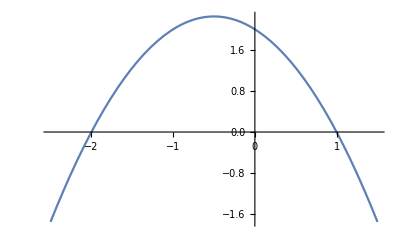

```mathematica
maxminint[f,-∞,∞]
```

```mathematica
f/.sol (*distancia máxima entre las 2 distancias*)
```

{2.25}

## 15

```mathematica
(*programa para máximos y mínimos*)
(*ejericio #13*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

```mathematica
f= 100(1+Cos[x])Sin[x];
```

Maximo en =  1.0472

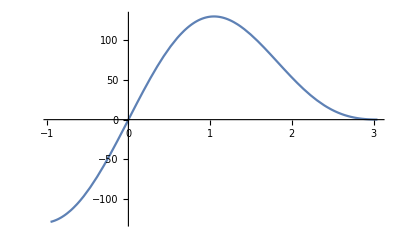

```mathematica
maxminint[f,0, π/2]
```

```mathematica
(x/.sol)  180/π
```

{60.}